```mathematica
ConverterEffic=FullSimplify[√(κμ κ)b/.Solve[{ϵ I ω a==ϵ I G/(√2)p-κ/2 a+I ϵ Ein,ϵ I ω p==ϵ I G/(√2)a+ϵ I Ω r-(Γ/2-ϵ I Δe)p,ϵ I ω r==ϵ I  Ω p-(γr/2-ϵ I Δr)r+ϵ I Gμ/(√2)b,ϵ I ω b==- ((γr+κμ)/2-ϵ I Δμ)b+ϵ I Gμ/(√2)r},{a,b,p,r}][[1]]];
```

```mathematica
assumptions=Element[{G,Gμ,κ,Γ,Δe,Δr,γr,κμ,Δμ,Ω,Ein,ϵ},PositiveReals]&&Element[ω,Reals];

Efficiency = FullSimplify[ComplexExpand[Abs[ConverterEffic]^2],assumptions]
```

(64 Ein^2 G^2 Gμ^2 ϵ^8 κ κμ Ω^2)/((4 Gμ^2 ϵ^3 (Δe κ-(Γ+κ) ω)+2 ϵ (Δμ-ω) (4 ϵ^2 (Δr-ω) (-Δe κ+(Γ+κ) ω)+γr (Γ κ+2 ϵ^2 (G^2+2 (Δe-ω) ω))+4 ϵ^2 κ Ω^2)+(-γr-κμ) (γr (-2 Δe ϵ κ+2 ϵ (Γ+κ) ω)-2 ϵ (Δr-ω) (Γ κ+2 ϵ^2 (G^2+2 (Δe-ω) ω))+8 ϵ^3 ω Ω^2))^2+(2 Gμ^2 ϵ^2 (Γ κ+2 ϵ^2 (G^2+2 (Δe-ω) ω))-(-γr-κμ) (4 ϵ^2 (Δr-ω) (-Δe κ+(Γ+κ) ω)+γr (Γ κ+2 ϵ^2 (G^2+2 (Δe-ω) ω))+4 ϵ^2 κ Ω^2)+2 ϵ (Δμ-ω) (γr (-2 Δe ϵ κ+2 ϵ (Γ+κ) ω)-2 ϵ (Δr-ω) (Γ κ+2 ϵ^2 (G^2+2 (Δe-ω) ω))+8 ϵ^3 ω Ω^2))^2)

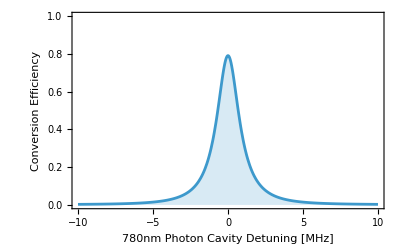

```mathematica
gopt=0.025;
gmm= 0.091;
Natoms = 5 10^5;
ΩUV = 0.03;
ΔUV = 1;
θUV = ArcTan[Abs[ΩUV/ΔUV]];
Nmm = Natoms (Sin[θUV])^2;
Nopt= Natoms (Cos[θUV])^2;
Gopt = gopt √Nopt;
Gmm = gmm √Nmm;
γopt = 6;
γmm = 0.100;
κopt = 10;
κmm = 10;
Ωb = 1.45 /2;
FBlue = 100;

parms={G->Gopt,Gμ->Gmm,κ->κopt,Γ->γopt,Δe->0,Δr->0.,γr->γmm,κμ->κmm,Δμ->0,Ω->√(FBlue/π) Ωb,Ein->1.,ϵ->1};
Plot[Efficiency/.parms,{ω,-10,10},PlotRange->{0,1},Frame->True,FrameLabel->{Style["780nm Photon Cavity Detuning [MHz]",14],Style["Conversion Efficiency",14]},Filling->Axis]
```

```mathematica
simplifications = {Δe->0,Δr->0,Δμ->0,Ein->1,ϵ->1};
SimpleEfficiency = FullSimplify[Efficiency /. simplifications, assumptions];
SimpleEfficiency
```

(64 G^2 Gμ^2 κ κμ Ω^2)/(4 ω^2 (Γ γr κ+2 Gμ^2 (Γ+κ)-4 (Γ+κ) ω^2+2 γr (G^2-2 ω^2)+4 κ Ω^2+(γr+κμ) (2 G^2+γr κ+Γ (γr+κ)-4 ω^2+4 Ω^2))^2+(2 Gμ^2 (2 G^2+Γ κ-4 ω^2)-4 ω^2 (2 G^2+γr κ+Γ (γr+κ)-4 ω^2+4 Ω^2)+(γr+κμ) (2 G^2 γr-4 (γr+κ) ω^2+Γ (γr κ-4 ω^2)+4 κ Ω^2))^2)

```mathematica
FullSimplify[SimpleEfficiency/. {ω-> 0}]
```

(64 G^2 Gμ^2 κ κμ Ω^2)/(((2 G^2+Γ κ) (2 Gμ^2+γr (γr+κμ))+4 κ (γr+κμ) Ω^2)^2)